# Unitarity Bound Plots.

## Formulae from 1805.07306.

```mathematica
(*Definitions from 1805.07306*)
λ[s_,mi2_, mj2_]:=1/s^2(s^2+mi2^2+mj2^2-2mi2 mj2 -2 s mi2 -2s mj2)(*eq.7*)
modp[s_,mi2_,mj2_]:=1/2 √(s*λ[s,mi2,mj2]) (*eq.8*)
Ei[s_,mi2_,mj2_]:=(s+mi2-mj2)/(2 √s) (*eq.8*)
ft[s_,m12_,m22_,m32_,m42_,m52_]:=1/s 1/(λ[s,m12,m22]*λ[s,m32,m42])^2 Log[(m12+m32-m52-2Ei[s,m12,m22]*Ei[s,m32,m42]+2modp[s,m12,m22]*modp[s,m32,m42])/(m12+m32-m52-2Ei[s,m12,m22]*Ei[s,m32,m42]-2modp[s,m12,m22]*modp[s,m32,m42])](*eq. 9*)
fu[s_,m12_,m22_,m32_,m42_,m52_]:=ft[s,m12,m22,m42,m32,m52](*eq. 9*)

a0[s_]:=-2^(1/2(delta12+delta34))/(16 π)((λ[s,m12,m22]*λ[s,m32,m42])^(1/4)(λ1234+(κ125*κ345)/(s-m52s))-κ135*κ245 *ft[s,m12,m22,m32,m42,m52t]-κ145*κ235*fu[s,m12,m22,m32,m42,m52u])(*eq. 10*)
```

## Kinematic Poles

```mathematica
(*If m1=m3 and m2=m4 and propagator is the same type*)
```

```mathematica
rootsMin = √m12+√m22+1/2(-√m52s+√((-4 √m12+√m52s)(-4 √m22+√m52s)))//N
```

√m12+√m22+0.5 (√((-4. √m12+√m52s) (-4. √m22+√m52s))-1. √m52s)

## Unitarity Bound Plots in Symmetric Phase.

### Couplings:

```mathematica
SymPhase={λσσσσ->3λσ-KroneckerDelta[F p,4]*c*((p F)(p F-1)(p F-2)(p F-3))/F^2, 
κσσσ->KroneckerDelta[F p,3]*(-(2c)/(2F)^2*(p F)/6(p F-1)(p F-2))};
```

{λσσσσ→3 λσ-(c p (-3+F p) (-2+F p) (-1+F p) 4,F p)/F,κσσσ→-(c p (-2+F p) (-1+F p) 3,F p)/(12 F)}

### Scattering σ σ -> σ σ :

```mathematica
(*Data from the scattering process. See 'The Question of Unitarity' on DropBox*)
(*This is σ σ->σ σ scattering.*)
ME={λ1234 -> λσσσσ,
κ125 -> κσσσ,
κ345 -> κσσσ,
κ135 -> κσσσ,
κ245 -> κσσσ,
κ145 -> κσσσ,
κ235 -> κσσσ,
delta12 -> 1,
delta34 -> 1,
m12 -> mσ2,
m22 ->mσ2,
m32 -> mσ2,
m42 ->mσ2,
m52u->mσ2,
m52t->mσ2,
m52s->mσ2};
```

#### Van der Woude

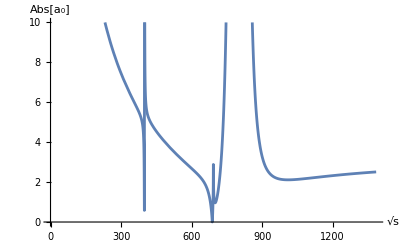

```mathematica
(*#1 Van der Woude point B*)
t1 = {mσ2->400^2,mη2->672^2,λσ->25.5,λa->15.2,c->4091, F->3,p->1,fpi->90*√(3/2)};
(*Would go from point rootsMin but it's actually larger than 4*pi*v*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.t1]],{rootS,0,4*π*fpi/.t1},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,10}]
(*Tc=145.8 and Tn=145.3*)
```

```mathematica
(*Technical Minimum s (eq. 15)*)
rootsMin/.ME/.t1
```

1200.

#### Ours

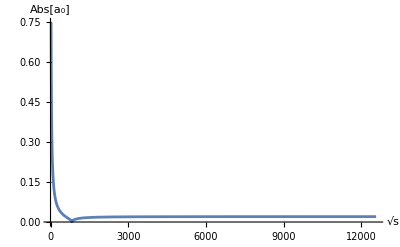

```mathematica
(*#2 one of our points*)
t2 = {mσ2->170000,mη2->100,λσ->0.17,λa->3.24,c->10^-10, F->6,p->1,fpi->1000};
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.{t2}]],{rootS,0,4π*fpi/.t2},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,.75}]
(*Tc=288 and Tn=250*)
```

```mathematica
(*Technical Minimum s (eq. 15)*)
rootsMin/.ME/.t2
```

1236.93

## Unitarity Bound Plots in Broken Phase.

### Couplings:

```mathematica
(*Calculated expressions for the vertices*)
BrokenPhase={λσσηη->3λσ+c fpi^(p F-4)((p F)(p F-1)(p F -2)(p F-3))/F^2,(*Numerical factor.?*)
			λσσσσ->3λσ-c fpi^(p F-4)((p F)(p F-1)(p F -2)(p F-3))/F^2,
			κσηη->2*F*(λσ-λa),
			κσσσ->6*F*λσ*fpi-c/(6 F^2)fpi^(p F-3)(p F)(p F-1)(p F-2)};
```

{λσσηη→(c fpi^(-4+F p) p (-3+F p) (-2+F p) (-1+F p))/F+3 λσ,λσσσσ→-(c fpi^(-4+F p) p (-3+F p) (-2+F p) (-1+F p))/F+3 λσ,κσηη→2 F (-λa+λσ),κσσσ→-(c fpi^(-3+F p) p (-2+F p) (-1+F p))/(6 F)+6 F fpi λσ}

### Scattering σ σ -> σ σ:

```mathematica
(*Data from the scattering process. See 'The Question of Unitarity' on DropBox*)
(*This is σ σ->σ σ scattering.*)
ME={λ1234 -> λσσσσ,
κ125 -> κσσσ,
κ345 -> κσσσ,
κ135 -> κσσσ,
κ245 -> κσσσ,
κ145 -> κσσσ,
κ235 -> κσσσ,
delta12 -> 1,
delta34 -> 1,
m12 -> mσ2,
m22 ->mσ2,
m32 -> mσ2,
m42 ->mσ2,
m52u->mσ2,
m52t->mσ2,
m52s->mσ2};
```

#### Van der Woude

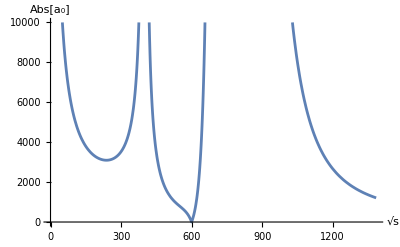

```mathematica
(*#1 Van der Woude point B*)
t1 = {mσ2->400^2,mη2->672^2,λσ->25.5,λa->15.2,c->4091, F->3,p->1,fpi->90*√(3/2)};
(*Would go from point rootsMin but it's actually larger than 4*pi*v*)
Plot[Abs[Re[a0[rootS^2]/.ME/.BrokenPhase/.t1]],{rootS,0,4*π*fpi/.t1},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,10000}]
(*Tc=145.8 and Tn=145.3*)
```

```mathematica
(*Technical Minimum s (eq. 15)*)
rootsMin/.ME/.t1
```

1200.

```mathematica
(*Comparison to MM's calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.t1
(*Comparison to Symmetric Phase in s->∞ limit:*)
(3*λσ)/(32 π)/.t1
(*As Fp=3, there is more subtlety for generic s. See 'VanDerWoudeUnitarity.nb'*)
```

0.76096

0.76096

#### Ours:

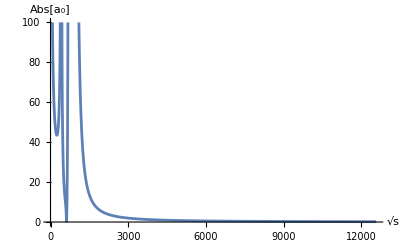

```mathematica
(*#2 one of our points*)
t2 = {mσ2->170000,mη2->100,λσ->0.17,λa->3.24,c->10^-10, F->6,p->1,fpi->1000};
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.BrokenPhase/.{t2}]],{rootS,0,4π*fpi/.t2},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,100}]
(*Tc=288 and Tn=250*)
```

```mathematica
(*Technical Minimum s (eq. 15)*)
rootsMin/.ME/.t2
```

1236.93

```mathematica
(*Comparison to MM's Calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.t2
(*Comparison to Symmetric Phase:*)
(3*λσ)/(32 π)/.t2
```

0.00508301

0.00507306

### Mixed Scattering σ η’->σ η’:

```mathematica
(*Data from the scattering process. See 'The Question of Unitarity' on DropBox*)
(*This is σ η'->σ η' scattering.*)
mixedME={λ1234 -> λσσηη,
κ125 -> κσηη,
κ345 -> κσηη,
κ135 -> κσσσ,
κ245 -> κσηη,
κ145 -> κσηη,
κ235 -> κσηη,
delta12 -> 0,
delta34 -> 0,
m12 -> mσ2,
m22 ->mη2,
m32 -> mσ2,
m42 -> mη2,
m52u->mη2,
m52t->mσ2,
m52s->mη2};
```

#### Van der Woude:

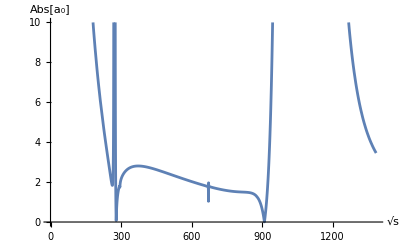

```mathematica
(*#1 Van der Woude point B*)
t1 = {mσ2->400^2,mη2->672^2,λσ->25.5,λa->15.2,c->4091, F->3,p->1,fpi->90*√(3/2)};
(*Would go from point rootsMin but it's actually larger than 4*pi*v*)
Plot[Abs[Re[a0[rootS^2]/.mixedME/.BrokenPhase/.t1]],{rootS,0,4*π*fpi/.t1},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,10}]
(*Tc=145.8 and Tn=145.3*)
```

```mathematica
(*Comparison to MM's calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.t1
(*Comparison to Symmetric Phase in s->∞ limit:*)
(3*λσ)/(32 π)/.t1
(*As Fp=3, there is more subtlety for generic s. See 'VanDerWoudeUnitarity.nb'*)
```

0.76096

0.76096

#### Ours:

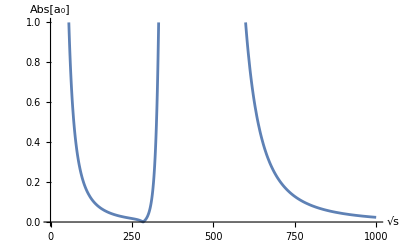

```mathematica
(*#2 one of our points*)
t2 = {mσ2->170000,mη2->100,λσ->0.17,λa->3.24,c->10^-10, F->6,p->1,fpi->1000};
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.mixedME/.BrokenPhase/.{t2}]],{rootS,0,fpi/.t2},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,1}]
(*Tc=288 and Tn=250*)
```

```mathematica
(*Comparison to MM's Calculation in s->∞ limit:*)
1/(32π)(3λσ+c*fpi^(F p-4)(((F p)(F p-1)(F p-2)(F p-3))/F^2))/.t2
(*Comparison to Symmetric Phase:*)
(3*λσ)/(32 π)/.t2
```

0.00508301

0.00507306